```mathematica
updateState::usage = "Updates CA loop state based on rule";
updateState[rule_,state_]:=(
 state[[1]]->CellularAutomaton[rule,state[[2]]](*Single evolution of rule*)
)

getReading::usage = "Measures the state of a given index";
getReading[state_,readindex_]:=(
state[[2]][[readindex]]
)

getCandidates::usage = "Creates all possible candidate states that can be represented with a given number of bits";
getCandidates[datasize_]:=(
cand = Tuples[{0,1},datasize];
Thread[cand->cand])

eliminateCandidates::usage = " Eliminates candidates that do not agree with the latest reading";
eliminateCandidates[candidates_,readindex_,reading_]:=(
Select[candidates,getReading[#,readindex]==reading&]
)


updateAllCandidates::usage = "Updates all candidate states";
updateAllCandidates[rule_,candidates_]:=(
updateState[rule,#1]&/@candidates
)

stepDecoder::usage = "Does a single step of the Decoder";
stepDecoder[rule_,candidates_,readindex_,reading_]:=(
updatedcandidates = updateAllCandidates[rule,candidates];
validcandidates = eliminateCandidates[updatedcandidates,readindex,reading])

encodeMasterState::usage = "Encodes data by reading a column of CA";
encodeMasterState[rule_,masterstate_,readindex_,nupdates_]:=(
CellularAutomaton[rule,masterstate,nupdates][[;;,readindex]])

decodeNoFirstUpdate::usage = "Decodes the data, should not technically take masterstate as argument";
decodeNoFirstUpdate[rule_,encodedsequence_,datasize_,readindex_]:=(
candidates = getCandidates[datasize];
n =1;
candidates = eliminateCandidates[candidates,readindex,encodedsequence[[n]]] ;(*Edge case*)
n=n+1;
While[Length[candidates]>1 && n≤Length[encodedsequence],
candidates = stepDecoder[rule,candidates,readindex,encodedsequence[[n]]];
(*Print[Length[candidates]];*)
n=n+1];
AppendTo[pr,n-1] (*return the dimension of the compressed data*)
(*{n-1,candidates}*)(*To verify correct data transferred*))

decodeWithFirstUpdate::usage = "Decodes the data, compares from first update";
decodeWithFirstUpdate[rule_,encodedsequence_,datasize_,readindex_]:=(
candidates = getCandidates[datasize];
n =1;
n=n+1; (*Because the first index or the read values is the true master state value*)
While[Length[candidates]>1 && n≤Length[encodedsequence],
candidates = stepDecoder[rule,candidates,readindex,encodedsequence[[n]]];
(*Print[Length[candidates]];*)
n=n+1];
AppendTo[pr,n-2] (*return the dimension of the compressed data*)
(*{n-1,candidates}*)(*To verify correct data transferred*))

getEncodingStatsForData[data_,nsamples_]:=(
rule := RandomInteger[255];
datasize = Length[data];
readindex := RandomInteger[{1,datasize}];
masterstate= data;
maxencodeseqlen = datasize/2; (*Currently at must compress to 50*)
encodedsequence := encodeMasterState[rule,masterstate,readindex,maxencodeseqlen ];
SetSharedVariable[pr];
pr={}; (*global? variable for parallel storage*)
ParallelDo[DecodeWithFirstUpdate[rule,encodedsequence,datasize,readindex],{i,nsamples}];
Select[pr,#<maxencodeseqlen&]/datasize
)
```

{0.58054,Null}

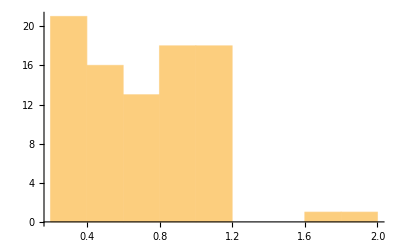

```mathematica
rule := RandomInteger[255];
datasize = 10;
readindex := RandomInteger[{1,datasize}];
masterstate:= RandomInteger[{0,1},datasize];
maxencodeseqlen = datasize*2;
encodedsequence := encodeMasterState[rule,masterstate,readindex,maxencodeseqlen ];
SetSharedVariable[pr]
pr={};
AbsoluteTiming@ParallelDo[decodeNoFirstUpdate[rule,encodedsequence,datasize,readindex],{i,100}]
Histogram[Select[pr,#<maxencodeseqlen&]/datasize]
```

{66.2022,Null}

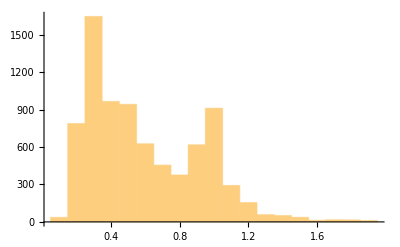

```mathematica
rule := RandomInteger[255];
datasize = 10;
readindex := RandomInteger[{1,datasize}];
masterstate:= RandomInteger[{0,1},datasize];
maxencodeseqlen = datasize*2;
encodedsequence := encodeMasterState[rule,masterstate,readindex,maxencodeseqlen ];
SetSharedVariable[pr]
pr={};
AbsoluteTiming@ParallelDo[DecodeWithFirstUpdate[rule,encodedsequence,datasize,readindex],{i,10000}]
Histogram[Select[pr,#<maxencodeseqlen&]/datasize]
```

```mathematica
datasize = 5;
masterstate:= RandomInteger[{0,1},datasize];
```

```mathematica
s = getEncodingStatsForData[masterstate,6];
Histogram[s]
```

CellularAutomaton::offg: The offset specification Integer[5] should be an integer or {offt, offx1, offx2, ... offxk}, where offt is present and k does not exceed 1, the number of spatial dimensions.

Part::partd: Part specification CellularAutomaton[165,{1,0,1,1,0,1,0,1,1,1},Integer[5]]⟦1;;All,7⟧ is longer than depth of object.

Part::partd: Part specification CellularAutomaton[90,{1,0,1,1,0,1,0,1,1,1},Integer[5]]⟦1;;All,8⟧ is longer than depth of object.

Part::partd: Part specification CellularAutomaton[152,{1,0,1,1,0,1,0,1,1,1},Integer[5]]⟦1;;All,10⟧ is longer than depth of object.

Part::partd: Part specification CellularAutomaton[198,{1,0,1,1,0,1,0,1,1,1},Integer[5]]⟦1;;All,10⟧ is longer than depth of object.

Part::partd: Part specification CellularAutomaton[59,{1,0,1,1,0,1,0,1,1,1},Integer[5]]⟦1;;All,5⟧ is longer than depth of object.

Part::partd: Part specification CellularAutomaton[53,{1,0,1,1,0,1,0,1,1,1},Integer[5]]⟦1;;All,4⟧ is longer than depth of object.

-Graphics-

```mathematica
Min[s]
```

1/10

Need to try technique for all data, random rules and indexes want best
 - We get the best compression for a certain amount of samples 
 - We see if the the best compression for a large amount different data makes sense

{1/10,1/10,1/10,1/10,3/20,1/10,1/10,1/10,1/10,1/10,1/20,1/10,1/10,1/10,1/10,1/10,1/20,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/20,1/20,1/10,1/10,1/10,1/10,1/20,1/10,1/10,1/10,1/10,1/10,1/10,1/20,1/20,1/20,1/10,1/20,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/20,1/10,1/10,1/20,1/10,1/10,1/10,1/10,1/10,1/20,1/10,1/20,1/10,1/10,1/10,1/10,1/10,1/10,1/20,1/10,1/20,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/20,1/20,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/20,1/10,1/10,1/10,1/10,1/10,1/20,1/10,1/20}

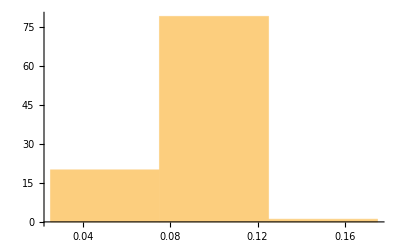

```mathematica
datasize = 20;
masterstate:= RandomInteger[{0,1},datasize];

minfordifferent = Table[Min[getEncodingStatsForData[masterstate,60]],100]
Histogram[minfordifferent]
```

```mathematica
Integer[4.5]
```

Integer[4.5]

```mathematica
2^5
```

32

```mathematica
0.15*20 + 5 +8
```

16.